```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions= Δk > 0 && k>0 && τ∈Reals &&τQ>0;
d[s_,z_] := ParabolicCylinderD[s,z];
z = Sqrt[Δk] * τ *Exp[I*Pi/4];
s = 1/(4*I*Δk);
vk =-(a*d[-s-1,- I  z]+ b *d [-s-1, I z]);
uk = Simplify[(-Δk τ vk+ 2 I D[vk,τ] )]
(*
a= 0;
b= ⅇ^(-π/(16 Δk))/(2 √Δk);
Δk = 1/(4*τQ Sin[k]^2);
τ = 4*τQ * Sin[k]*(-t/τQ+Cos[k]); *)
```

2 (-1)^(1/4) √Δk (a ParabolicCylinderD[ⅈ/(4 Δk),-(-1)^(3/4) √Δk τ]-b ParabolicCylinderD[ⅈ/(4 Δk),(-1)^(3/4) √Δk τ])

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

2 ⅇ^(-π/(8 Δk)) π (Im[1/Gamma[1-ⅈ/(4 Δk)]]^2+Re[1/Gamma[1-ⅈ/(4 Δk)]]^2)

ⅇ^(π/(8 Δk))/(Δk τ^2)

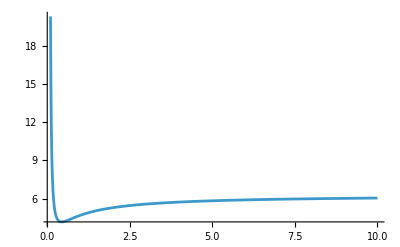

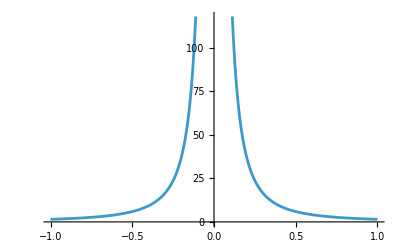

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
(*Now we show that the condition vk(-inf)=0 gives a and b 
We do that first by showing that a needs to be 0 
We plot |vk|^2 in the asymptotic limit that tau->-inf for b = 0 and a= 0 respectively
We first see that a asymptotes for a nonzero constant for all deltak. b asymptotes to 0.
Thus in the limit we say that a = 0, and we can find b through normalization*)
vinit = Asymptotic[Abs[vk]^2,τ->-Infinity];
vA= Limit[Asymptotic[vinit/.b->0/.a->1,τ->-Infinity],τ->-Infinity]
vB = Assuming[{τ<0},Simplify[vinit/.b->1/.a->0 ]]
Plot[vA,{Δk,0.1,10},PlotRange->All]
Plot[vB/.Δk->1,{τ,-1,1}]
```

```mathematica
(*To compute normalization, we simply set |uk|^2 = 1 as its initial condition requires*)
a= 0;
uinit = Assuming[{b!=0},Limit[uk,τ->-Infinity]]/.Interval[{0,2 Pi}]->0;
binit=b/. Solve[uinit==1,b]//First;
FullSimplify[ComplexExpand[binit]]
FullSimplify[ComplexExpand[Abs[binit]]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (-1)^(3/4) ⅇ^(-π/(16 Δk)) Δk^(-(ⅈ+4 Δk)/(8 Δk))

ⅇ^(-π/(16 Δk))/(2 √Δk)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
(*Now we are able to get the fully simplified vk and uk*)
b =FullSimplify[ComplexExpand[Abs[binit]]]
vk=FullSimplify[vk]
uk=FullSimplify[uk]
```

ⅇ^(-π/(16 Δk))/(2 √Δk)

-(ⅇ^(-π/(16 Δk)) ParabolicCylinderD[-1+ⅈ/(4 Δk),(-1)^(3/4) √Δk τ])/(2 √Δk)

-(-1)^(1/4) ⅇ^(-π/(16 Δk)) ParabolicCylinderD[ⅈ/(4 Δk),(-1)^(3/4) √Δk τ]

```mathematica
Δk= (4*τQ * Sin[k]^2)^(-1);
τ = 4*τQ*Sin[k]*(-t/τQ+Cos[k]);
ufinal = Simplify[uk/.t->0]
vfinal = Simplify[vk/.t->0]
```

-(-1)^(1/4) ⅇ^(-1/4 π τQ Sin[k]^2) ParabolicCylinderD[ⅈ τQ Sin[k]^2,(-1)^(3/4) √τQ Abs[Csc[k]] Sin[2 k]]

-(ⅇ^(-1/4 π τQ Sin[k]^2) √τQ ParabolicCylinderD[-1+ⅈ τQ Sin[k]^2,(-1)^(3/4) √τQ Abs[Csc[k]] Sin[2 k]])/Abs[Csc[k]]

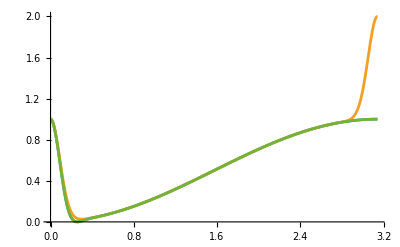

```mathematica
Plot[{Simplify[Abs[ufinal]^2]/.τQ->10,(1-Cos[k])/2 + E^(-2 Pi τQ Sin[k]^2)/.τQ->10, 1-Abs[vfinal]^2 /.τQ->10},{k,0,Pi}]
```

```mathematica
g = Simplify[ufinal*Conjugate[vfinal]]
```

```mathematica
1/Abs[Csc[k]](-1)^(1/4) ⅇ^(-1/2 π τQ Sin[k]^2) √τQ Conjugate[ParabolicCylinderD[-1+ⅈ τQ Sin[k]^2,(-1)^(3/4) √τQ Abs[Csc[k]] Sin[2 k]]] ParabolicCylinderD[ⅈ τQ Sin[k]^2,(-1)^(3/4) √τQ Abs[Csc[k]] Sin[2 k]]
Phi = Pi/4 + Δk * τ^2 /2 + Log[Δk]/4/Δk+ Log[τ]/2/Δk - Arg[Gamma[1+ I/4/Δk]]/.t->0
```

1/Abs[Csc[k]](-1)^(1/4) ⅇ^(-1/2 π τQ Sin[k]^2) √τQ Conjugate[ParabolicCylinderD[-1+ⅈ τQ Sin[k]^2,(-1)^(3/4) √τQ Abs[Csc[k]] Sin[2 k]]] ParabolicCylinderD[ⅈ τQ Sin[k]^2,(-1)^(3/4) √τQ Abs[Csc[k]] Sin[2 k]]

π/4-Arg[Gamma[1+ⅈ τQ Sin[k]^2]]+2 τQ Cos[k]^2+τQ Log[Csc[k]^2/(4 τQ)] Sin[k]^2+2 τQ Log[4 τQ Cos[k] Sin[k]] Sin[k]^2

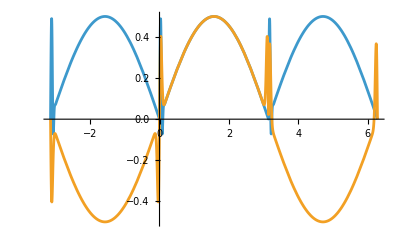

```mathematica
Plot[{Re[g]/.τQ->100,1/2 Sin[k]+Sign[k]*Exp[-Pi τQ Sin[k]^2]* Sqrt[1-E^(-Pi τQ Sin[k]^2 )  ]/.τQ->100},{k,-Pi,2 Pi}]
```

```mathematica
vB
```